# μB xsec - GiBUU and GENIE

```mathematica
ymax=10^11;
ymin=10^4;
ticoy=Flatten[{Table[{y,("10")^ToString[y]},{y,Log[10,ymin],Log[10,ymax]}],Table[{y," "},{y,Log[10,2ymin],Log[10,ymax]}],Table[{y," "},{y,Log[10,3ymin],Log[10,ymax]}],Table[{y," "},{y,Log[10,4ymin],Log[10,ymax]}],Table[{y," "},{y,Log[10,5ymin],Log[10,ymax]}],Table[{y," "},{y,Log[10,6ymin],Log[10,ymax]}],Table[{y," "},{y,Log[10,7ymin],Log[10,ymax]}],Table[{y," "},{y,Log[10,8ymin],Log[10,ymax]}],Table[{y," "},{y,Log[10,9ymin],Log[10,ymax]}]},1];
```

## MicroBooNE xsec data

```mathematica
μBdat=Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/microB_data.txt","Data"];
```

```mathematica
Needs["ErrorBarPlots`"];
μBplot=Table[{{μBdat[[i,3]],μBdat[[i,4]]/μBdat[[i,3]]},ErrorBar[{μBdat[[i,1]]-μBdat[[i,3]],μBdat[[i,2]]-μBdat[[i,3]]},μBdat[[i,5]]/μBdat[[i,3]]]},{i,1,Length[μBdat]}];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

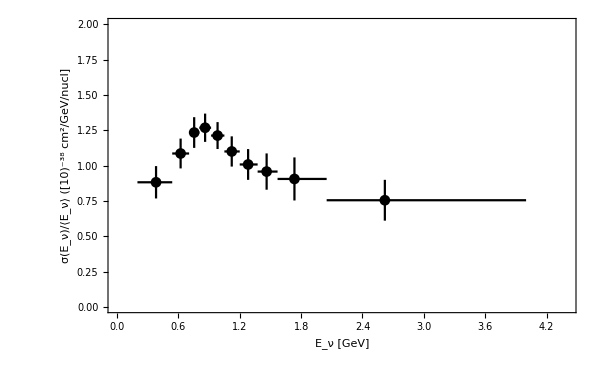

```mathematica
grid=Grid[{{Graphics[{EdgeForm[Black],Directive[Opacity[1,Black]],PointSize[0.3],Point[{0,0}]},ImageSize->20],Style["Data",14,Black]},{Graphics[{EdgeForm[Black],Directive[Opacity[1,Orange]],Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["GiBUU",14,Black]},{Graphics[{EdgeForm[Black],Directive[Opacity[1,Purple]],Dashed,Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["MicroBooNE 2022",14,Black]}},Frame->True,Background-> White];


μB=ErrorListPlot[{μBplot},PlotRange->{{0,4.4},{0,2.0}},Frame-> True,FrameLabel-> {{"σ(E_ν)/⟨E_ν⟩ ([10)^-38 cm^2/GeV/nucl]",None},{"E_ν [GeV]","MicroBooNE 5.3 × 10^19POT"}},PlotStyle-> Black, LabelStyle->{Black,Bold,18},
FrameTicksStyle-> Directive[Black,18,Thick],PlotRangePadding->None,
ImageSize-> 600]

(*/⟨Subscript[E, ν]⟩ /GeV/*)
```

```mathematica
Export["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/microB-xsec2.png",Out[84]];
```

## Flux

```mathematica
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/microB_flux.dat","Data"];
bnbflux=Interpolation[Table[{%[[i,1]]+(%[[i,2]]-%[[i,1]])/2,Log[10,%[[i,3]]]},{i,1,Length[%]}]];
```

```mathematica
totflux=NIntegrate[10^bnbflux[x],{x,0.025,6}]
```

5.85028×10^9

```mathematica
flux=Table[1/totflux*NIntegrate[10^bnbflux[x],{x,μBdat[[i,1]],μBdat[[i,2]]}],{i,1,Length[μBdat]}]
```

{0.256032,0.140541,0.0820952,0.0872925,0.0875395,0.0844132,0.0755236,0.0549211,0.0488276,0.0150697}

```mathematica
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/numuflux_BNB.dat","Data"];
bnbflux2=Interpolation[Table[{%[[i,1]],Log[10,%[[i,2]]]},{i,1,Length[%]}]];
```

```mathematica
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/numu_flux_microB.dat","Data"];
bnbflux3=Interpolation[Table[{%[[i,1]],Log[10,%[[i,2]]]},{i,1,Length[%]}]];
```

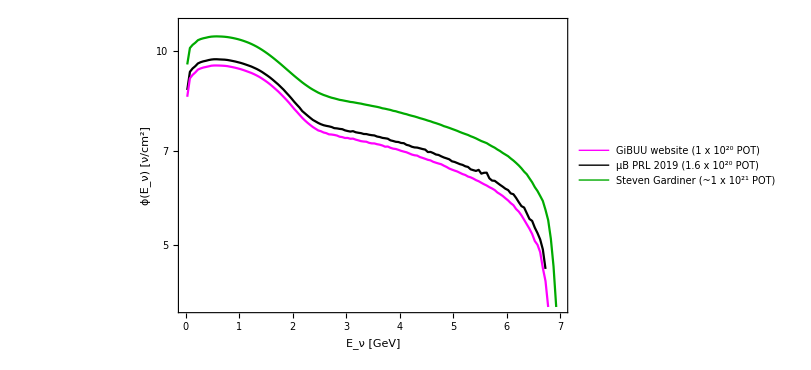

```mathematica
gridflux=Grid[{{Graphics[{EdgeForm[Black],Directive[Opacity[1,Magenta]],Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["GiBUU website (1 x 10^20 POT)",14,Black]},{Graphics[{EdgeForm[Black],Directive[Opacity[1,Black]],Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["μB PRL 2019 (1.6 x 10^20 POT)",14,Black]},{Graphics[{EdgeForm[Black],Directive[Opacity[1,Darker[Green]]],Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["Steven Gardiner (~1 x 10^21 POT)",14,Black]}},Frame->True,Background-> White];
ListLogPlot[{bnbflux,bnbflux2,bnbflux3},Joined->True ,PlotRange->{{0,7},{4,11}},Frame-> True,FrameLabel-> {{"ϕ(E_ν) [ν/cm^2]",None},{"E_ν [GeV]","BNB ν_μ Flux"}},PlotStyle->{ Black,Magenta,Darker[Green]}, LabelStyle->{Black,Bold,18},FrameTicks->{{ticoy,Automatic},{{0,1,2,3,4,5,6,7},Automatic}},
FrameTicksStyle-> Directive[Black,18,Thick],PlotRangePadding->None,
ImageSize-> 600,Epilog->{Text[gridflux,{2.2,1.7}]}]
```

```mathematica
Export["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/results/BNB-fluxes.png",Out[96]];
```

## GiBUU Reconstructed Neutrino Events

```mathematica
μBsmear=Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/microB_smearing.txt","Data"];
```

```mathematica
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/numu_microB/files/microB_CCQE_rw_60_GiBUU.txt","Data"];
GirwQE=Table[%[[i,2]]/(100),{i,1,Length[%]}];
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/numu_microB/files/microB_CCRES_rw_60_GiBUU.txt","Data"];
GirwRES=Table[%[[i,2]]/(100),{i,1,Length[%]}];
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/numu_microB/files/microB_CCMEC_rw_60_GiBUU.txt","Data"];
GirwMEC=Table[%[[i,2]]/(100),{i,1,Length[%]}];
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/numu_microB/files/microB_CCDIS_rw_60_GiBUU.txt","Data"];
GirwDIS=Table[%[[i,2]]/100,{i,1,Length[%]}];
```

```mathematica
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/numu_microB/files/microB_CC_10_GiBUU.txt","Data"];
GiTot=Table[%[[i,2]]/(100),{i,1,Length[%]}];
```

```mathematica
σtot=Table[GiTot[[i]]/flux[[i]],{i,1,Length[μBdat]}]
σqe=Table[GirwQE[[i]]/flux[[i]],{i,1,Length[μBdat]}];
σres=Table[GirwRES[[i]]/flux[[i]],{i,1,Length[μBdat]}];
σdis=Table[GirwDIS[[i]]/flux[[i]],{i,1,Length[μBdat]}];
σmec=Table[GirwMEC[[i]]/flux[[i]],{i,1,Length[μBdat]}];
```

{0.368735,0.76106,0.869981,0.974697,1.10648,1.26729,1.36428,1.50511,1.57756,2.25355}

```mathematica
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/numu_microB/files/microB_CCQE_rw_10_GiBUU.txt","Data"];
GirwQE2=Table[%[[i,2]]/(100),{i,1,Length[%]}];
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/numu_microB/files/microB_CCRES_rw_10_GiBUU.txt","Data"];
GirwRES2=Table[%[[i,2]]/(100),{i,1,Length[%]}];
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/numu_microB/files/microB_CCMEC_rw_10_GiBUU.txt","Data"];
GirwMEC2=Table[%[[i,2]]/(100),{i,1,Length[%]}];
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/numu_microB/files/microB_CCDIS_rw_10_GiBUU.txt","Data"];
GirwDIS2=Table[%[[i,2]]/100,{i,1,Length[%]}];
```

```mathematica
σqe2=Table[GirwQE2[[i]]/flux[[i]],{i,1,Length[μBdat]}];
σres2=Table[GirwRES2[[i]]/flux[[i]],{i,1,Length[μBdat]}];
σdis2=Table[GirwDIS2[[i]]/flux[[i]],{i,1,Length[μBdat]}];
σmec2=Table[GirwMEC2[[i]]/flux[[i]],{i,1,Length[μBdat]}];
```

#### Reconstructed events

```mathematica
GiRecowo=μBsmear.(σtot);
GiRecowh=μBsmear.(σqe+σres+σdis+σmec);
GiRecowh2=μBsmear.(σqe2+σres2+σdis2+σmec2);
```

```mathematica
GiBUU=Table[{μBdat[[i,3]],GiRecowo[[i]]/μBdat[[i,3]]},{i,1,Length[μBdat]}]
```

{{0.3818,1.0181},{0.622,1.12751},{0.7546,1.16968},{0.8615,1.15788},{0.9833,1.12925},{1.122,1.07274},{1.282,1.02645},{1.463,1.00757},{1.735,0.974828},{2.619,0.824827}}

```mathematica
GiBUUrwght=Table[{μBdat[[i,3]],GiRecowh[[i]]/μBdat[[i,3]]},{i,1,Length[μBdat]}]
```

{{0.3818,0.810216},{0.622,1.01869},{0.7546,1.17758},{0.8615,1.22783},{0.9833,1.19893},{1.122,1.11538},{1.282,1.04882},{1.463,1.02145},{1.735,0.982886},{2.619,0.825558}}

```mathematica
GiBUUrwght2=Table[{μBdat[[i,3]],GiRecowh2[[i]]/μBdat[[i,3]]},{i,1,Length[μBdat]}]
```

{{0.3818,0.774313},{0.622,1.04111},{0.7546,1.19019},{0.8615,1.21362},{0.9833,1.17968},{1.122,1.10671},{1.282,1.05936},{1.463,1.06884},{1.735,1.08177},{2.619,0.948402}}

## GiBUU Results from Shweta

```mathematica
{{0.3818,1.0181},{0.622,1.1275},{0.7546,1.169},{0.8615,1.1578},{0.9833,1.129},{1.122,1.0727},{1.282,1.0264},{1.463,1.00757},{1.735,0.9748},{2.619,0.8248}};
GiBUUshweta=Table[{%[[i,1]],%[[i,2]]},{i,1,Length[%]}];
```

```mathematica
{{0.3818,0.8102},{0.622,1.0187},{0.7546,1.1775},{0.8615,1.228},{0.9833,1.1989},{1.122,1.115},{1.282,1.0488},{1.463,1.02144},{1.735,0.9828},{2.619,0.8255}};
GiBUUshwetarw=Table[{%[[i,1]],%[[i,2]]},{i,1,Length[%]}];
```

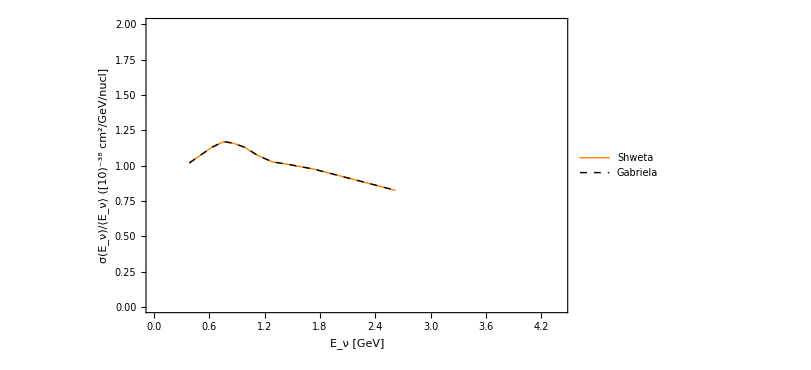

```mathematica
grida=Grid[{{Graphics[{EdgeForm[Black],Directive[Opacity[1,Orange]],Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["Shweta",14,Black]},{Graphics[{EdgeForm[Black],Directive[Opacity[1,Black]],Dashed,Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["Gabriela",14,Black]}},Frame->True,Background-> White];a=ListPlot[{GiBUUshweta,GiBUU},PlotRange->{{0,4.4},{0,2}},Frame-> True,FrameLabel-> {{"σ(E_ν)/⟨E_ν⟩ ([10)^-38 cm^2/GeV/nucl]",None},{"E_ν [GeV]","GiBUU - MicroBooNE"}},PlotStyle->{{Orange,Thick},{Black,Dashed,Thick}},Joined->True
, LabelStyle->{Black,Bold,18},
FrameTicksStyle-> Directive[Black,18,Thick],PlotRangePadding->None,
ImageSize-> 600,Epilog-> {Text[grida,{3.6,1.6}]}]
```

```mathematica
Export["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/numu_microB/figures/numu_GiBUU_gs_microB.png",Out[170]];
```

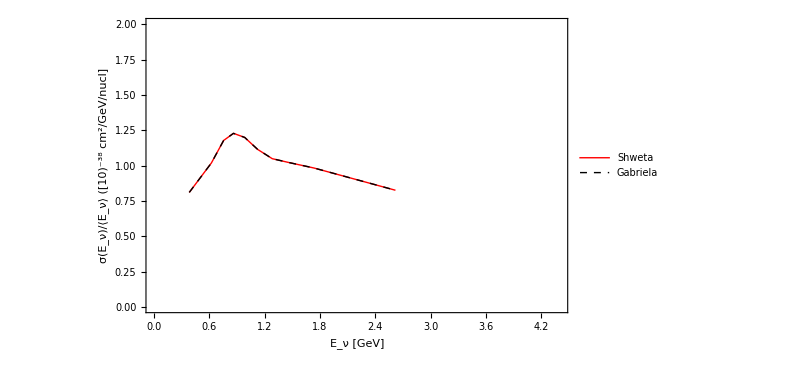

```mathematica
gridrb=Grid[{{Graphics[{EdgeForm[Black],Directive[Opacity[1,Red]],Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["Shweta",14,Black]},{Graphics[{EdgeForm[Black],Directive[Opacity[1,Black]],Dashed,Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["Gabriela",14,Black]}},Frame->True,Background-> White];
b=ListPlot[{GiBUUshwetarw,GiBUUrwght},PlotRange->{{0,4.4},{0,2}},Frame-> True,FrameLabel-> {{"σ(E_ν)/⟨E_ν⟩ ([10)^-38 cm^2/GeV/nucl]",None},{"E_ν [GeV]","GiBUU reweighted - MicroBooNE"}},PlotStyle->{{Red,Thick},{Black,Dashed,Thick}},Joined->True
, LabelStyle->{Black,Bold,18},
FrameTicksStyle-> Directive[Black,18,Thick],PlotRangePadding->None,
ImageSize-> 600,Epilog-> {Text[gridrb,{3.6,1.6}]}]
(*/⟨Subscript[E, ν]⟩ /GeV*)
```

```mathematica
Export["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/numu_microB/figures/numu_GiBUU_rw_gs_microB.png",Out[189]];
```

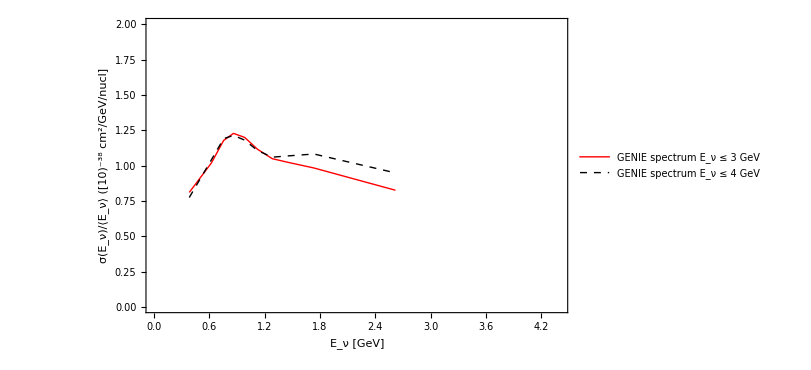

```mathematica
gridrc=Grid[{{Graphics[{EdgeForm[Black],Directive[Opacity[1,Red]],Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["GENIE spectrum E_ν ≤ 3 GeV",14,Black]},{Graphics[{EdgeForm[Black],Directive[Opacity[1,Black]],Dashed,Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["GENIE spectrum E_ν ≤ 4 GeV",14,Black]}},Frame->True,Background-> White];
c=ListPlot[{GiBUUrwght,GiBUUrwght2},PlotRange->{{0,4.4},{0,2}},Frame-> True,FrameLabel-> {{"σ(E_ν)/⟨E_ν⟩ ([10)^-38 cm^2/GeV/nucl]",None},{"E_ν [GeV]","GiBUU reweighted - MicroBooNE"}},PlotStyle->{{Red,Thick},{Black,Dashed,Thick}},Joined->True
, LabelStyle->{Black,Bold,18},
FrameTicksStyle-> Directive[Black,18,Thick],PlotRangePadding->None,
ImageSize-> 600,Epilog-> {Text[gridrc,{3.3,1.6}]}]
(*/⟨Subscript[E, ν]⟩ /GeV*)
```

```mathematica
Export["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/numu_microB/figures/numu_GiBUU_rw_2spec_microB.png",Out[202]];
```

## GiBUU 2019 vs GiBUU 2021

```mathematica
totflux2=NIntegrate[10^bnbflux2[x],{x,0.025,6}];
flux2=Table[1/totflux2*NIntegrate[10^bnbflux2[x],{x,μBdat[[i,1]],μBdat[[i,2]]}],{i,1,Length[μBdat]}];
```

```mathematica
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/GiBUU_2021_2019/microB_CC_GiBUU_2019.txt","Data"];
GiTot2019=Table[%[[i,2]]/(100),{i,1,Length[%]}];
σtot2019=Table[GiTot2019[[i]]/flux2[[i]],{i,1,Length[μBdat]}];
GiRecowo2019=μBsmear.(σtot2019);
```

```mathematica
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/GiBUU_2021_2019/microB_CC_GiBUU_2021.txt","Data"];
GiTot2021=Table[%[[i,2]]/(100),{i,1,Length[%]}];
σtot2021=Table[GiTot2021[[i]]/flux2[[i]],{i,1,Length[μBdat]}];
GiRecowo2021=μBsmear.(σtot2021);
```

```mathematica
GiBUU2019=Table[{μBdat[[i,3]],GiRecowo2019[[i]]/μBdat[[i,3]]},{i,1,Length[μBdat]}];
GiBUU2021=Table[{μBdat[[i,3]],GiRecowo2021[[i]]/μBdat[[i,3]]},{i,1,Length[μBdat]}];
```

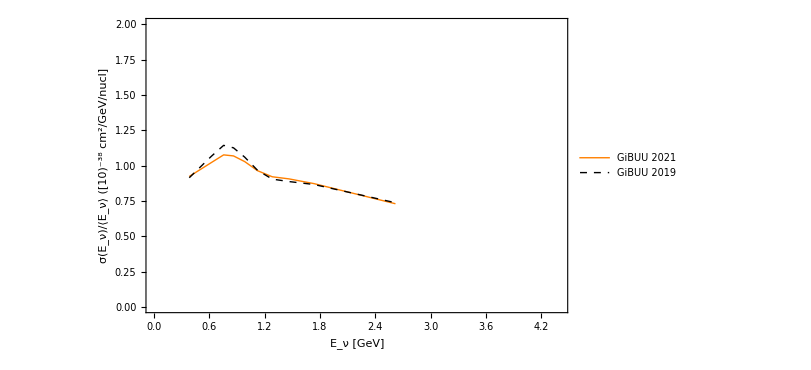

```mathematica
gridv=Grid[{{Graphics[{EdgeForm[Black],Directive[Opacity[1,Orange]],Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["GiBUU 2021",14,Black]},{Graphics[{EdgeForm[Black],Directive[Opacity[1,Black]],Dashed,Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["GiBUU 2019",14,Black]}},Frame->True,Background-> White];v=ListPlot[{GiBUU2021,GiBUU2019},PlotRange->{{0,4.4},{0,2}},Frame-> True,FrameLabel-> {{"σ(E_ν)/⟨E_ν⟩ ([10)^-38 cm^2/GeV/nucl]",None},{"E_ν [GeV]","GiBUU 1 x 10^20 POT - MicroBooNE"}},PlotStyle->{{Orange,Thick},{Black,Dashed,Thick}},Joined->True
, LabelStyle->{Black,Bold,18},
FrameTicksStyle-> Directive[Black,18,Thick],PlotRangePadding->None,
ImageSize-> 600,Epilog-> {Text[gridv,{3.6,1.6}]}]
```

```mathematica
Export["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/GiBUU_2021_2019/numu_GiBUU_2versions_microB.png",Out[287]];
```

```mathematica
Test=Table[{μBdat[[i,3]],GiRecowo2021[[i]]/GiRecowo[[i]]},{i,1,Length[μBdat]}]
```

{{0.3818,0.905602},{0.622,0.909399},{0.7546,0.921968},{0.8615,0.922593},{0.9833,0.909027},{1.122,0.896325},{1.282,0.89406},{1.463,0.89712},{1.735,0.896056},{2.619,0.889703}}

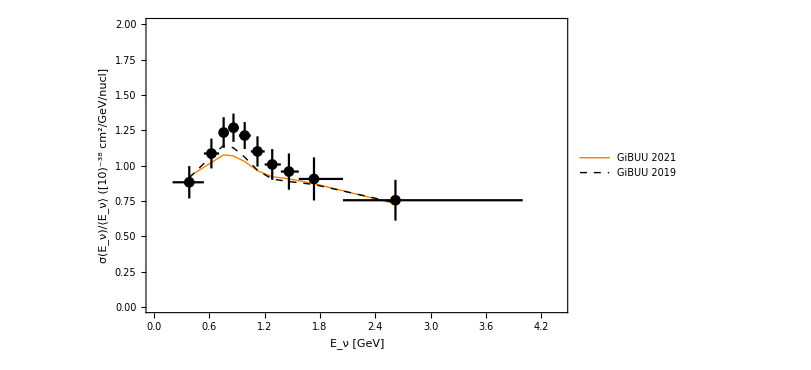

```mathematica
Show[{v,μB}]
```

```mathematica
Export["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/GiBUU_2021_2019/numu_GiBUU_2versions_wdat_microB.png",Out[81]];
```

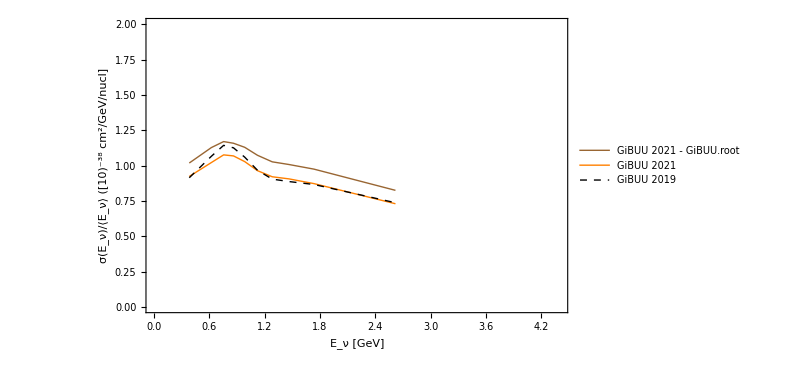

```mathematica
gridv2=Grid[{{Graphics[{EdgeForm[Black],Directive[Opacity[1,Brown]],Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["GiBUU 2021 - GiBUU.root",14,Black]},{Graphics[{EdgeForm[Black],Directive[Opacity[1,Orange]],Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["GiBUU 2021",14,Black]},{Graphics[{EdgeForm[Black],Directive[Opacity[1,Black]],Dashed,Thick,Line[{{0,0},{1.0,0}}]},ImageSize->20],Style["GiBUU 2019",14,Black]}},Frame->True,Background-> White];v2=ListPlot[{GiBUU,GiBUU2021,GiBUU2019},PlotRange->{{0,4.4},{0,2}},Frame-> True,FrameLabel-> {{"σ(E_ν)/⟨E_ν⟩ ([10)^-38 cm^2/GeV/nucl]",None},{"E_ν [GeV]","GiBUU 1 x 10^20 POT - MicroBooNE"}},PlotStyle->{{Brown,Thick},{Orange,Thick},{Black,Dashed,Thick}},Joined->True
, LabelStyle->{Black,Bold,18},
FrameTicksStyle-> Directive[Black,18,Thick],PlotRangePadding->None,
ImageSize-> 600,Epilog-> {Text[gridv2,{3.4,1.5}]}]
```

```mathematica
Export["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/GiBUU_2021_2019/numu_GiBUU_2versions_Gi.root_microB.png",Out[93]];
```

## GiBUU Results from MicroBooNE paper

```mathematica
Import["/home/gstenico/Desktop/SBND_GiBUU/GiBUU-GENIE/GiBUU_paper.csv","Data"]
GiBUUpaper=Table[{%[[i,1]],%[[i,2]]},{i,1,Length[%]}]
```